{{AR→1,AL→-(3 ⅈ (-1+ⅇ^4))/(ⅈ+2 √2-ⅈ ⅇ^4+2 √2 ⅇ^4),BR→(2 (-2 ⅈ+√2) ⅇ^4)/(ⅈ+2 √2-ⅈ ⅇ^4+2 √2 ⅇ^4),BL→(2 ⅈ (-4 ⅈ+√2))/((-ⅈ+√2) (ⅈ+2 √2-ⅈ ⅇ^4+2 √2 ⅇ^4)),CR→-(4 (2 ⅈ+√2) ⅇ^(2-2 ⅈ √2))/((-1-ⅈ √2) (ⅈ+2 √2-ⅈ ⅇ^4+2 √2 ⅇ^4)),CL→0}}

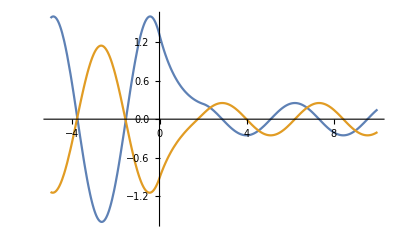

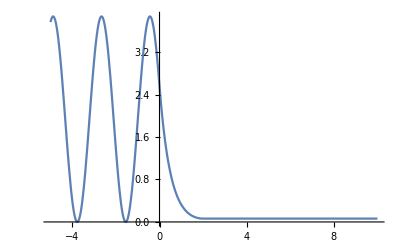

```mathematica
m=1;
Ē=1;
ћ=1;
V=3/2;
k0=(√(2m Ē))/ћ;
k1=(√(2m(Ē-V)))/ћ;
l=2;
s=Solve[AR+AL==BR+BL&&I k0(AR-AL)==I k1(BR-BL)&&BR Exp[I k1 l]+BL Exp[-I k1 l]==CR Exp[I k0 l]+CL Exp[-I k0 l]&&I k1(BR Exp[I k1 l]-BL Exp[-I k1 l])==I k0(CR Exp[I k0 l]-CL Exp[-I k0 l])&&AR==1&&CL==0,{AR,AL,BR,BL,CR,CL}]

Plot[{Piecewise[{{Re[AR Exp[I k0 x]+AL Exp[-I k0 x]]/.s,x<0},{Re[BR Exp[I k1 x]+BL Exp[-I k1 x]]/.s,0<x<l},{Re[CR Exp[I k0 x]+CL Exp[-I k0 x]]/.s,x>l}}],Piecewise[{{Im[AR Exp[I k0 x]+AL Exp[-I k0 x]]/.s,x<0},{Im[BR Exp[I k1 x]+BL Exp[-I k1 x]]/.s,0<x<l},{Im[CR Exp[I k0 x]+CL Exp[-I k0 x]]/.s,x>l}}]},{x,-5,10},PlotRange->All]
Plot[Piecewise[{{Abs[AR Exp[I k0 x]+AL Exp[-I k0 x]]^2/.s,x<0},{Abs[BR Exp[I k1 x]+BL Exp[-I k1 x]]^2/.s,0<x<l},{Abs[CR Exp[I k0 x]+CL Exp[-I k0 x]]^2/.s,x>l}}],{x,-5,10},PlotRange->All]
```